```mathematica
ps1[x_]:=Style[x,Blue,Bold,18]
```

```mathematica
StyledListLinePlot[x_,y_]:=ListLinePlot[x,PlotStyle->{Red,Orange,Darker[Green],Blue},AxesLabel->{ps1["U,V"],ps1["I,uA"]},LabelStyle->Directive[Blue,Bold,FontSize->18],PlotMarkers->{●,15},GridLines->{Range[-1,1,0.1],Range[0,1000,1]},PlotLegends->Placed[Table[ps1[y[[i]]],{i,Length[y]}],Above],ImageSize->Full]
```

```mathematica
StyledListLinePlot[x_]:=StyledListLinePlot[x,{ps1["I"],ps1["I_ionic"]}]
```

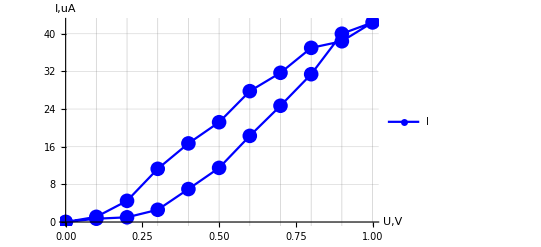

```mathematica
Kz01iv=({{0, 0}, {0.1, .7}, {0.2, 1}, {0.3, 2.6}, {0.4, 7}, {0.5, 11.5}, {0.6, 18.3}, {0.7, 24.7}, {0.8, 31.4}, {0.9, 40}, {1, 42.4}, {0.9, 38.4}, {0.8, 37}, {0.7, 31.7}, {0.6, 27.8}, {0.5, 21.2}, {0.4, 16.7}, {0.3, 11.3}, {0.2, 4.5}, {0.1, 1.1}, {0, 0}});StyledListLinePlot[Kz01iv]
```

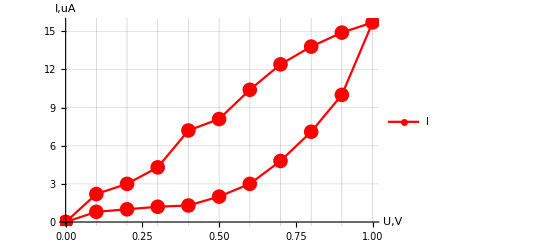

```mathematica
Kz02iv=({{0, 0}, {0.1, .8}, {0.2, 1}, {0.3, 1.2}, {0.4, 1.3}, {0.5, 2}, {0.6, 3}, {0.7, 4.8}, {0.8, 7.1}, {0.9, 10}, {1, 15.7}, {0.9, 14.9}, {0.8, 13.8}, {0.7, 12.4}, {0.6, 10.4}, {0.5, 8.1}, {0.4, 7.2}, {0.3, 4.3}, {0.2, 3}, {0.1, 2.2}, {0, 0}});StyledListLinePlot[{Kz02iv}]
```

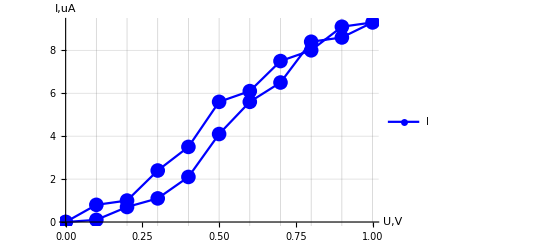

```mathematica
Mz94iv=({{0, 0}, {0.1, .1}, {0.2, .7}, {0.3, 1.1}, {0.4, 2.1}, {0.5, 4.1}, {0.6, 5.6}, {0.7, 6.5}, {0.8, 8.4}, {0.9, 8.6}, {1, 9.3}, {0.9, 9.1}, {0.8, 8}, {0.7, 7.5}, {0.6, 6.1}, {0.5, 5.6}, {0.4, 3.5}, {0.3, 2.4}, {0.2, 1}, {0.1, .8}, {0, 0}});StyledListLinePlot[Mz94iv]
```

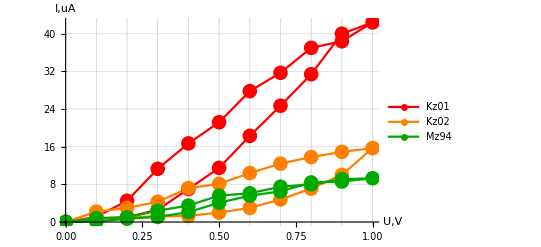

```mathematica
StyledListLinePlot[{Kz01iv,Kz02iv,Mz94iv},{"Kz01","Kz02","Mz94"}]
```

```mathematica
FRlist[list_]:=Apply[Divide,Drop[Drop[list,1],-1],{1}]*10^6
```

```mathematica
RKz01iv=FRlist[Kz01iv]
```

{142857.,200000.,115385.,57142.9,43478.3,32786.9,28340.1,25477.7,22500.,23584.9,23437.5,21621.6,22082.,21582.7,23584.9,23952.1,26548.7,44444.4,90909.1}

```mathematica
RKz02iv=FRlist[Kz02iv]
```

{125000.,200000.,250000.,307692.,250000.,200000.,145833.,112676.,90000.,63694.3,60402.7,57971.,56451.6,57692.3,61728.4,55555.6,69767.4,66666.7,45454.5}

```mathematica
RMz94iv=FRlist[Mz94iv]
```

{1.×10^6,285714.,272727.,190476.,121951.,107143.,107692.,95238.1,104651.,107527.,98901.1,100000.,93333.3,98360.7,89285.7,114286.,125000.,200000.,125000.}

```mathematica
Min[RKz02iv]
```

45454.5

```mathematica
Max[RKz02iv]
```

307692.

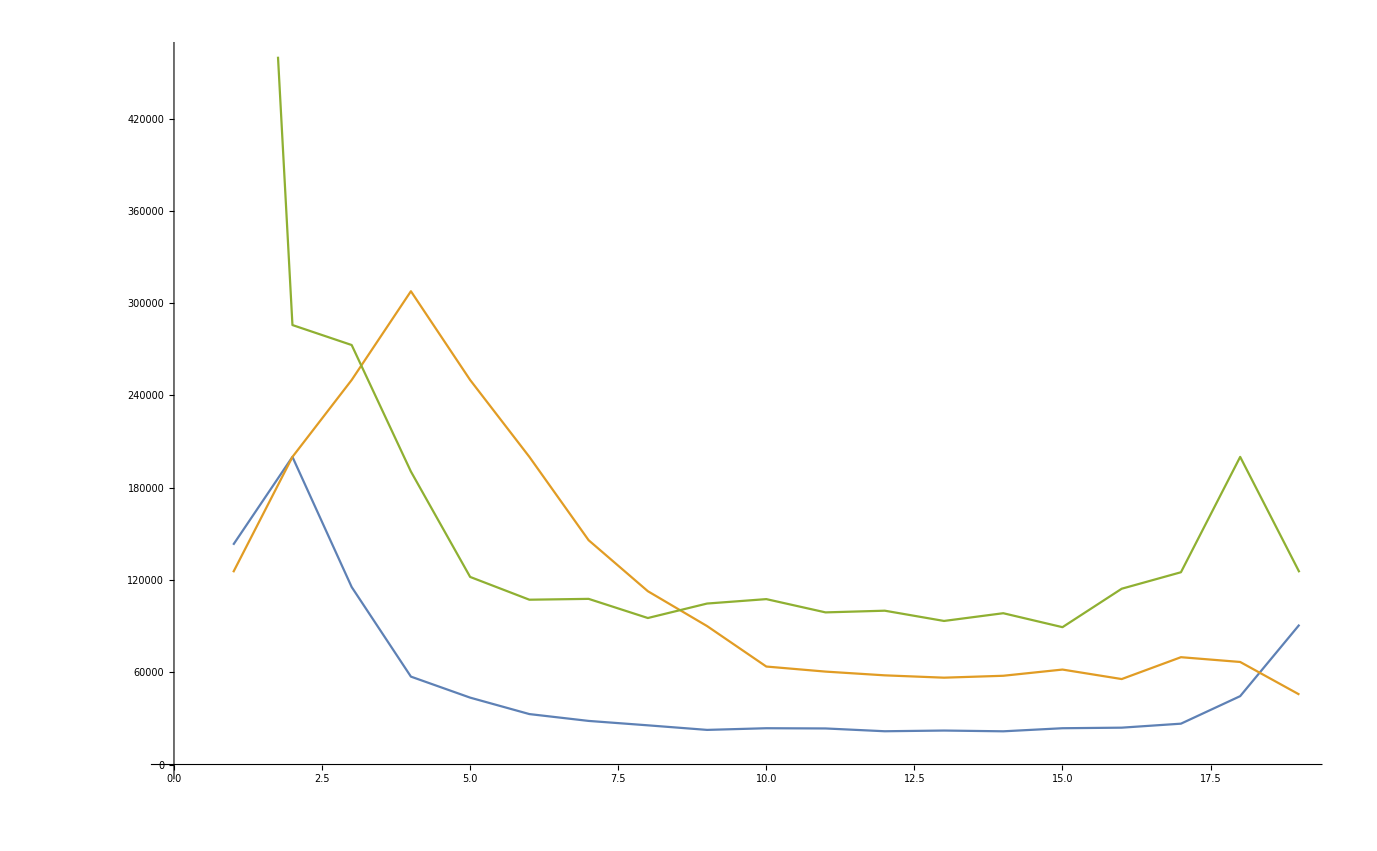

```mathematica
ListLinePlot[{RKz01iv,RKz02iv,RMz94iv}]
```

```mathematica
50*10^-6*6.2
```

0.00031

```mathematica
N[1/(3*10^5)-0.9/(3*10^5-3*10^4)]
```

0.

```mathematica
N[0.4/307692]
```

1.3×10^-6

```mathematica
0.5/250000
```

2.×10^-6

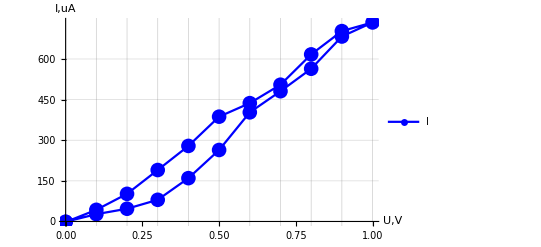

```mathematica
KzE01iv=({{0, -1}, {0.1, 27}, {0.2, 47}, {0.3, 80}, {0.4, 160}, {0.5, 264}, {0.6, 403}, {0.7, 481}, {0.8, 564}, {0.9, 683}, {1, 735}, {0.9, 703}, {0.8, 617}, {0.7, 505}, {0.6, 437}, {0.5, 387}, {0.4, 279}, {0.3, 190}, {0.2, 102}, {0.1, 43}, {0, -2}});StyledListLinePlot[KzE01iv]
```